```mathematica
Off[General::spell1]
```

```mathematica
boxsize=4000;
order=4;
levels=11;

nameBase1="SF_CaseIIL"<>ToString[boxsize];
nameBase2="O"<>ToString[order]<>"l"<>ToString[levels]<>"/";
file="u.Y";

num={33,37,65,73,129,145};

test=False;

dir="/home/juanpabv/Documents/ngrproj/codes/OllipticID/exe/Conv";

(*
dir="/home/pablo/Olliptic/exe/Conv";
*)
(*
dir="/home/pablo/Documentos/Olliptic_Test/Dirichlet/Poisson/6th/Conv"
*)
```

```mathematica
SetDirectory[
dir<>nameBase1<>nameBase2<>"/"
]
Nmax=Length[num];

u={};
v={};
h={};

If[
test,
format={Number,Number,Number};,
format={Number,Number};
]



For[
i=Nmax,

i≥1,

Infile=nameBase1<>"R"<>ToString[i]<>nameBase2<>file;
utmp=ReadList[Infile,format];
size=Length[utmp];

u=Join[{Table[{utmp[[j,1]],utmp[[j,2]]},{j,size}]},u];

If[test,
v=Join[{Table[{utmp[[j,1]],Abs[utmp[[j,3]]]},{j,size}]},v],
];

h=Join[{N[boxsize/(num[[i]]-1)]},h];

i-=1
]
```

/home/juanpabv/Documents/ngrproj/codes/OllipticID/exe/ConvSF_CaseIIL4000O4l11

```mathematica
fu=Table[Interpolation[u[[i]],InterpolationOrder->order+2],{i,Nmax}];

If[test,
fv=Table[Interpolation[v[[i]],InterpolationOrder->order+2],{i,Nmax}]
];
xmin=Min[u[[1,All,1]]];
xmax=Max[u[[1,All,1]]];
```

```mathematica
pi=order+1;
pf=order;
While[Abs[pi-pf] > 0.0001,

pi=pf;
α=Table[(h[[Nmax]]/h[[i]])^pi,{i,Nmax-1}];
uL1=Table[

1/(1-α[[i]])Abs[
Integrate[fu[[i]][x],{x,xmin,xmax} ]-
Integrate[ fu[[Nmax]][x],{x,xmin,xmax}]],

{i,Nmax-1} ];
data=Table[{Log[h[[i]]],Log[uL1[[i]]]},{i,Nmax-1}];
fitLine=Fit[data,{1,x},x];
pf=fitLine[[2,1]]
]

pf
Export[
"uL1.dat",
data,
"Table"
]

If[test,
vL1=Table[
Integrate[fv[[i]][x],{x,xmin,xmax} ],
{i,Nmax} ];
Export[
"vL1.dat",
Table[{Log[h[[i]]],Log[vL1[[i]]]},{i,Nmax}],
"Table"
]

]
```

2.67116

uL1.dat

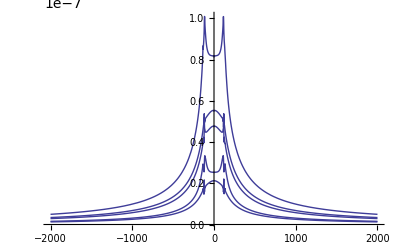

```mathematica
Plot[

Table[

Abs[(fu[[i]][x]-fu[[Nmax]][x])/(h[[i]]^pf-h[[Nmax]]^pf)]

,{i,Nmax-1}],

{x,xmin,xmax},PlotRange->All]
```

```mathematica
-1/(2π)375^2∫_0^(2π) (∫_0^π Sin[2 θ]^2 Cos[2ϕ]^2 Sin[θ]ⅆθ)ⅆϕ//N
-1/(2π)∫_0^(2π) (∫_0^π 1ⅆθ)ⅆϕ
%//N
∫_0^(2π) 1ⅆϕ//N
```

-75000.

-π

-3.14159

6.28319

```mathematica
TrigExpand[Cos[2θ]]
```

Cos[θ]^2-Sin[θ]^2